```mathematica
(* π/4 *) 

$alpha = π/6;
$beta = π/6;
$R = 10;
$r = 1;
$RSurface = 100;
$Tolerance = 5/100;

$zWalecSurface[x_,y_] := 1/2 (1/$RSurface x^2);
$zTorusTool[x_,y_] :=  1/2 ((1/$r) x^2 + (1/($r + ($R/Sin[$alpha])))y^2);
```

Z Walec Surface: x^2/200

Z Torus Tool: 1/2 (x^2+y^2/21)

Z Tangent Diff: -x^2/200+1/2 (x^2+y^2/21)

D Walec Surface: (1/100 | 0
0 | 0)

D Torus Tool: (1 | 0
0 | 1/21)

D Torus Rotated Tool: (0.761905 | 0.412393
0.412393 | 0.285714)

D Tangent Diff: (0.751905 | 0.412393
0.412393 | 0.285714)

Width Along Y: 1.59787

Width Along X: 2.59213

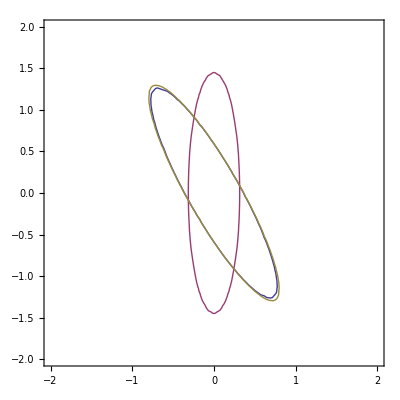

```mathematica
$zTangentDiff[x_,y_] := $zTorusTool[x,y] - $zWalecSurface[x,y];

$DWalec = 2({{$zWalecSurface[1,0], 0}, {0, $zWalecSurface[0,1]}});
$DTorus = 2({{$zTorusTool[1,0], 0}, {0, $zTorusTool[0,1]}});
$DTorusRotated = RotationMatrix[$beta].$DTorus. Transpose[RotationMatrix[$beta]];

$DDiff =$DTorusRotated - $DWalec;

$ZWalec = 1/2*{x,y}.$DWalec.{x,y};
$ZTorus = 1/2{x,y}.$DTorus.{x,y};
$ZTorusRotated = 1/2{x,y}.$DTorusRotated.{x,y};
$ZDiff = 1/2*{x,y}.$DDiff.{x,y};

v1 ={0,1};
(* < Make a function here > *)
$v = v1;
$w = {wx,wy};
$sol = Solve[{$w.$DDiff.$w/2 == $Tolerance, $v.$DDiff.$w  ==0},$w];
$w = $w/.$sol[[1]];
widthY= N[2*{-$v[[2]], $v[[1]]}.$w];
(* </ Make a function here >*)

v2 ={1,0};
(* < Make a function here > *)
$v = v2;
$w = {wx,wy};
$sol = Solve[{$w.$DDiff.$w/2 == $Tolerance, $v.$DDiff.$w  ==0},$w];
$w = $w/.$sol[[2]];
widthX = N[2*{-$v[[2]], $v[[1]]}.$w];
(* </ Make a function here >*)

Print["Z Walec Surface: ", $zWalecSurface[x,y]]
Print["Z Torus Tool: ", $zTorusTool[x,y]]
Print["Z Tangent Diff: ", $zTangentDiff[x,y]]

Print["D Walec Surface: ", MatrixForm[$DWalec]]
Print["D Torus Tool: ", MatrixForm[$DTorus]]
Print["D Torus Rotated Tool: ", N[MatrixForm[$DTorusRotated]]]
Print["D Tangent Diff: ", N[MatrixForm[$DDiff]]]

Print["Width Along Y: ", widthY]
Print["Width Along X: ", widthX]

$a = 2;
Show[ContourPlot[{$ZTorusRotated==$Tolerance, 
$ZTorus==$Tolerance,
$ZDiff==$Tolerance
},
{x,-$a,$a}, 
{y, -$a,$a}]]
```

```mathematica
X
```

X